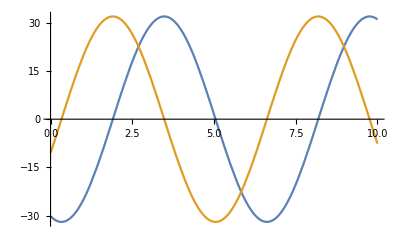

```mathematica
sol=NDSolveValue[{y''[t]+y[t]==0,y[2]==3,y[8]==-6},{y[t],y'[t]},{t,0,10}];
Plot[sol,{t,0,10}]
```

```mathematica
Plot3D[x^2+y^2,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Grad[x^2+y^2,{x,y}]
```

{2 x,2 y}

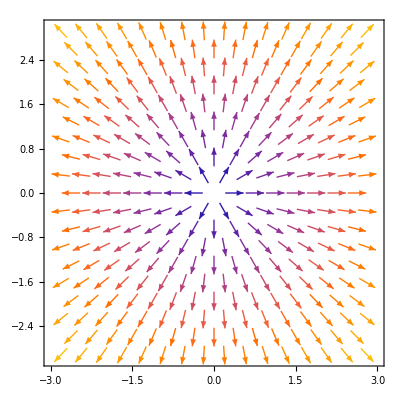

```mathematica
VectorPlot[{2 x,2 y},{x,-3,3},{y,-3,3}]
```

```mathematica
Div[{2 x,2 y},{x,y}]
```

4

```mathematica
Curl[{2 x,2 y},{x,y}]
```

0

```mathematica
Laplacian[x^2+y^2,{x,y}]
```

4

```mathematica
sol1=NDSolveValue[{∇_{x,y}^2 f[x,y]+f[x,y]==x E^y,DirichletCondition[f[x,y]==Sin[x ]Cos[y],True]},f[x,y],{x,y}∈Disk[{0,0},2]];
Plot3D[sol1,{x,-2.,2.},{y,-2.,2.}]
```

-Graphics3D-

```mathematica
Plot3D[x E^y,{x,-2.,2.},{y,-2.,2.}]
```

-Graphics3D-